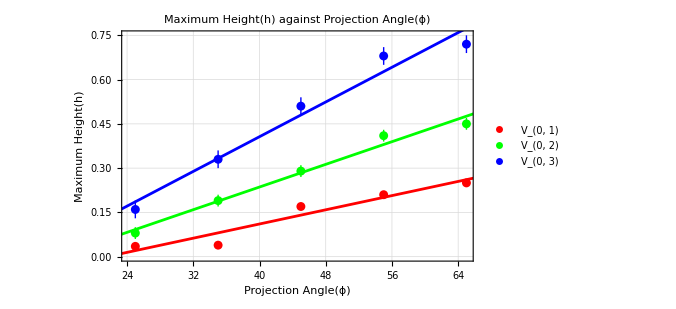
-Graphics-
V_(0, 1): y==0.00601 x-0.12965
V_(0, 2): y==0.0096 x-0.148
V_(0, 3): y==0.0147 x-0.1815

```mathematica
(*Define the datasets*)V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

(*Add error values to the datasets*)
errorV1=0.01; (*You can change this value based on your data*)
errorV2=0.02; (*You can change this value based on your data*)
errorV3=0.03; (*You can change this value based on your data*)

V1WithErrors={#[[1]],Around[#[[2]],errorV1]}&/@V1;
V2WithErrors={#[[1]],Around[#[[2]],errorV2]}&/@V2;
V3WithErrors={#[[1]],Around[#[[2]],errorV3]}&/@V3;

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines with error bars*)
combinedPlot=Show[ListPlot[{V1WithErrors,V2WithErrors,V3WithErrors},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle(ϕ)","Maximum Height(h)"},GridLines->Automatic,PlotLabel->"Maximum Height(h) against Projection Angle(ϕ)",ImageSize->500];

(*Display the plot with equations*)
Column[{combinedPlot,Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

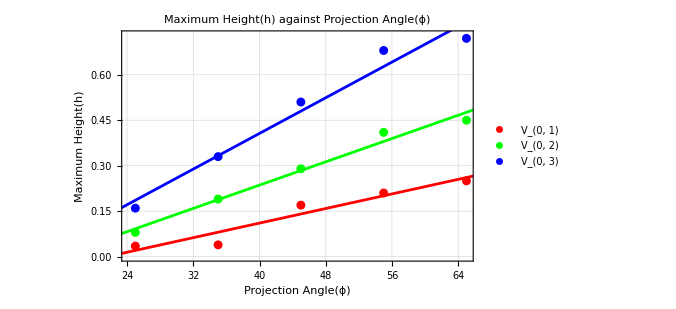
-Graphics-
V_(0, 1): y==0.00601 x-0.12965
V_(0, 2): y==0.0096 x-0.148
V_(0, 3): y==0.0147 x-0.1815

```mathematica
(*Define the datasets*)
V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

V1error={{25,Around[0.035,0.01]},{35,Around[0.039,0.01]},{45,Around[0.170,0.01]},{55,Around[0.210,0.01]},{65,Around[0.250,0.01]}};
V2error={{25,Around[0.080,0.01]},{35,Around[0.190,0.01]},{45,Around[0.290,0.01]},{55,Around[0.410,0.01]},{65,Around[0.450,0.01]}};
V3error={{25,Around[0.160,0.01]},{35,Around[0.330,0.01]},{45,Around[0.510,0.01]},{55,Around[0.680,0.01]},{65,Around[0.720,0.01]}};

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines*)
Column[{combinedPlot=Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle(ϕ)","Maximum Height(h)"},GridLines->Automatic,PlotLabel->"Maximum Height(h) against Projection Angle(ϕ)",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

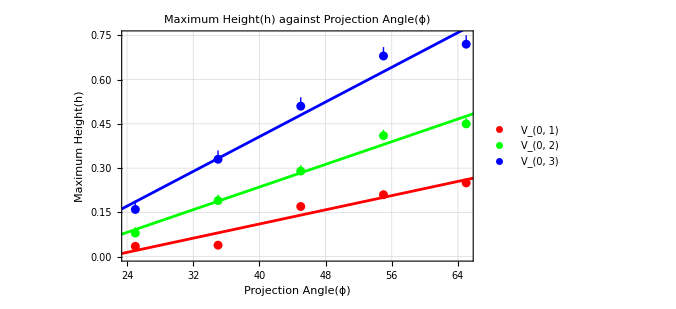
-Graphics-
V_(0, 1): y==0.00601 x-0.12965
V_(0, 2): y==0.0096 x-0.148
V_(0, 3): y==0.0147 x-0.1815

```mathematica
(*Define the datasets*)V1={{25,0.035},{35,0.039},{45,0.170},{55,0.210},{65,0.250}};
V2={{25,0.080},{35,0.190},{45,0.290},{55,0.410},{65,0.450}};
V3={{25,0.160},{35,0.330},{45,0.510},{55,0.680},{65,0.720}};

(*Add error values to the datasets*)
errorV1={{0,0.01},{0,0.01}}; (*Horizontal and vertical errors for V1*)
errorV2={{0,0.02},{0,0.02}}; (*Horizontal and vertical errors for V2*)
errorV3={{0,0.03},{0,0.03}}; (*Horizontal and vertical errors for V3*)

V1WithErrors={#[[1]],Around[#[[2]],errorV1]}&/@V1;
V2WithErrors={#[[1]],Around[#[[2]],errorV2]}&/@V2;
V3WithErrors={#[[1]],Around[#[[2]],errorV3]}&/@V3;

(*Fit linear models to the data*)
fitV1=LinearModelFit[V1,x,x];
fitV2=LinearModelFit[V2,x,x];
fitV3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitV1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fitV2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fitV3["BestFit"]]];

(*Plot the data and the best-fit lines with error bars*)
combinedPlot=Show[ListPlot[{V1WithErrors,V2WithErrors,V3WithErrors},PlotStyle->{Red,Green,Blue},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 2\)]\)","\!\(\*SubscriptBox[\(V\), \(0, 3\)]\)"}],Plot[{fitV1[x],fitV2[x],fitV3[x]},{x,0,90},PlotStyle->{Red,Green,Blue},PlotRange->{{0,90},Automatic}],Frame->True,FrameLabel->{"Projection Angle(ϕ)","Maximum Height(h)"},GridLines->Automatic,PlotLabel->"Maximum Height(h) against Projection Angle(ϕ)",ImageSize->500];

(*Display the plot with equations*)
Column[{combinedPlot,Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(0, 1\)]\): ",eq1}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 2\)]\): ",eq2}],Row[{"\!\(\*SubscriptBox[\(V\), \(0, 3\)]\): ",eq3}]}]}]
```

```mathematica
V1error={
{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]}};
V2error={
{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]}};
V3error={
{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]},{Around[,],Around[,]}};
```

```mathematica
Show[ListPlot[{V1error,V2error,V3error},PlotStyle->{Red,Green,Blue},
```